```mathematica
(*Basic CNN to classify MNIST database*)
ClearAll["Global`*"];
(*First we load the data*)
trainingData=ResourceData["MNIST","TrainingData"];
```

```mathematica
testData=ResourceData["MNIST","TestData"];
```

```mathematica
(*Have a look at the data*)
Length[trainingData]
```

60000

```mathematica
trainingData[[1]]
```

-Graphics-→0

```mathematica
ex=Keys[trainingData[[1]]](*example of image from the database*)
```

-Graphics-

```mathematica
ImageDimensions[ex]
```

{28,28}

```mathematica
(*Hence, dimensions of input images to the network are 28 x 28 pixels*)
```

```mathematica
(*We see that training and test data stored as associations*)
(*********************************************************************)
(*Now we start building the network; let's look again at the structure of the basic CNN discussed in the lecture*)
```

```mathematica
conv1=ConvolutionLayer[6,5,"Input"->{1,28,28}];(*6 feature maps, kernel size 5x5; we also specify size of input images*)
conv1In=NetInitialize[conv1](*Initialise layer; it assigns random weights and a random bias*)
```

ConvolutionLayer[<>]

```mathematica
(*Let's see the effect of this layer to one input image from the database*)
(*But first we need to "encode" the image so that it has the format expected by the convolutional layer. The convolutional layer is expecting a tensor (array) of dimensions 1 x 28 x 28*)
```

```mathematica
inputEx=Keys[trainingData[[1]]](*example of an image to give as input to conv layer*)
```

-Graphics-

```mathematica
imageenc=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}](*encode to transform the input image to the expected format*)
```

NetEncoder[<>]

```mathematica
inputExEnc=imageenc[inputEx];(*encoded input image, ready to be input to the layer*)
```

```mathematica
outputEx=conv1In[inputExEnc];(*output from layer*)
```

```mathematica
Dimensions[outputEx](*6 matrices, each one has size 24x24; these are our feature maps*)
```

{6,24,24}

```mathematica
outputEx[[1]]//Dimensions
```

{24,24}

```mathematica
(*Visualise output (feature maps)*)
Magnify[Table[Image[outputEx[[i]]],{i,1,6}],2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Visualise the weights of the layer*)
kernels1=NetExtract[conv1In,"Weights"];
```

```mathematica
Map[ImageAdjust@Image[#,Interleaving->False]&,Normal@kernels1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Here is a non-elegant but easier way to understand the last command*)
```

```mathematica
Dimensions[kernels1]
```

{6,1,5,5}

```mathematica
kernels1[[1]]//Normal
```

{{{0.296981,0.221052,0.00842446,-0.222936,0.0263331},{-0.147724,-0.0693819,0.167015,-0.36141,-0.251785},{-0.0786703,-0.17639,0.358533,-0.0816388,0.180343},{0.230554,-0.0855302,-0.0811076,-0.0181606,0.00315855},{0.119225,-0.238737,-0.0542767,0.136142,0.0911813}}}

```mathematica
Flatten[kernels1[[1]],1]//Normal
```

{{0.296981,0.221052,0.00842446,-0.222936,0.0263331},{-0.147724,-0.0693819,0.167015,-0.36141,-0.251785},{-0.0786703,-0.17639,0.358533,-0.0816388,0.180343},{0.230554,-0.0855302,-0.0811076,-0.0181606,0.00315855},{0.119225,-0.238737,-0.0542767,0.136142,0.0911813}}

```mathematica
Image[%]
```

-Graphics-

```mathematica
kernels1Flat=Table[Flatten[kernels1[[k]],1],{k,1,6}];
```

```mathematica
kernels1Im=Image/@Normal[kernels1Flat]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust/@kernels1Im
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*These are the 6 kernels used to generate the 6 feature maps in the first convolutional layer*)
(*Now let's get the biases*)
NetExtract[conv1In,"Biases"]//Normal
```

{0.,0.,0.,0.,0.,0.}

```mathematica
(*The next layer is the pooling layer*)
```

```mathematica
pool1=PoolingLayer[{2,2},2](*size 2x2, stride=2*)
```

PoolingLayer[<>]

```mathematica
pool1[{{{1,2,3},{4,5,6},{7,8,9}}}](*check working of the layer*)
```

{{{5.}}}

```mathematica
(*Join first and second layer*)
```

```mathematica
net1=NetChain[{conv1,pool1}]
```

NetChain[<>]

```mathematica
net1b=NetChain[Association["conv1"->conv1,"pool1"->pool1]]
```

NetChain[<>]

```mathematica
(*Now initialise net1b*)
net1bInit=NetInitialize[net1b]
```

NetChain[<>]

```mathematica
(*apply it to our example encoded image*)
output2=net1bInit[inputExEnc];
```

```mathematica
(*visualise result*)
Dimensions[output2]
```

{6,12,12}

```mathematica
Magnify[Table[Image[output2[[i]]],{i,1,6}],2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Now let's add the activation function layer after convolution, and after the pooling, add the 3 next layers: the 2nd convolutional layer, followed by activation and another pooling layer*)
net2=NetChain[{conv1,ElementwiseLayer[Ramp],pool1,ConvolutionLayer[12,5],ElementwiseLayer[Ramp],PoolingLayer[{2,2},2],ElementwiseLayer[Ramp]}]
```

NetChain[<>]

```mathematica
testData[[1]][[2]]//Head
```

Integer

```mathematica
(*Now we need to vectorise the output: FlattenLayer and feed it into a fully connected NN (classifier)*)
(*Also we need Net Decoder for final classification*)

dec=NetDecoder[{"Class",{0,1,2,3,4,5,6,7,8,9}}];(*essentially, this function evaluates which of the 10 final outputs has the largest value, and it gives the corresponding class*)
net3:=NetChain[{conv1,ElementwiseLayer[Ramp],pool1,ConvolutionLayer[12,5],ElementwiseLayer[Ramp],PoolingLayer[{2,2},2],FlattenLayer[],LinearLayer[10],ElementwiseLayer[Ramp],SoftmaxLayer[]},"Input"->imageenc,"Output"->dec]
```

```mathematica
(*We could have used net2 and just concatenate it to the new parts; in the summary net2 would have appeared as NetGraph*)
net3Init=NetInitialize[net3]
```

NetChain[<>]

```mathematica
(*Now we input our example image to the network and look at the output. Since we attached the image encoder to the input port of the network, now can apply the network directly to the raw example image.*)
output3=net3Init[inputEx]
```

9

```mathematica
(* Since we have not trained the network yet (weights and biases are random) the network does not recognise the digit in the image.*)

(*Training*************************************************)
```

```mathematica
net3Train=NetTrain[net3,trainingData,All,ValidationSet->testData]
```

NetTrain Results
summary | ,,  batches:9380  rounds:10  time:1.9min  examples/s:5319
data | ,,  training examples:60000  validation examples:10000  processed examples:600320  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.  error:42.2%
validation | ,,  loss:9.99×10^-1  error:41.8%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
(*Notice the option All so that an object is created, that stores information also about the training process*)
```

```mathematica
finalnet=net3Train["TrainedNet"]
```

NetChain[<>]

```mathematica
(*this gives us the trained network*)
```

```mathematica
net3Train["Properties"]
```

{ArraysLearningRateMultipliers,BatchesPerRound,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

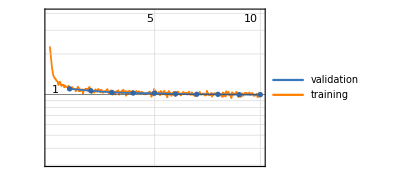
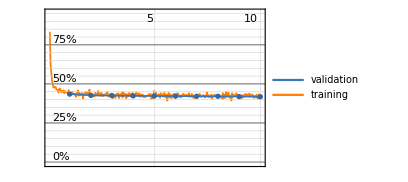
<|Loss→ | rounds
loss | -Graphics-,ErrorRate→ | rounds
error rate | -Graphics-|>

```mathematica
net3Train["FinalPlots"]
```

```mathematica
net3Train["ValidationMeasurements"]
```

<|Loss→0.998641,ErrorRate→0.4181|>

```mathematica
trainingData[[1]]
```

-Graphics-→0

```mathematica
(*Comparison with LeNet, which is slightly more complex*)
```

```mathematica
net4=NetTrain[NetModel["LeNet"],trainingData,All,ValidationSet->testData]
```

NetTrain Results
summary | ,,  batches:9380  rounds:10  time:5.0min  examples/s:1982
data | ,,  training examples:60000  validation examples:10000  processed examples:600320  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:6.86×10^-3  error:0.227%
validation | ,,  loss:3.56×10^-2  error:0.870%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
finalLeNet=net4["TrainedNet"]
```

NetChain[<>]

```mathematica
finalLeNet[inputEx]
```

0

```mathematica
finalnet[inputEx]
```

0

```mathematica
Information[finalnet,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
Information[finalnet,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
finalnet[[1]]
```

ConvolutionLayer[<>]

```mathematica
(*Evaluate performance of the network*)
randTest=RandomSample[testData,10]
```

{-Graphics-→5,-Graphics-→9,-Graphics-→9,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→6,-Graphics-→0,-Graphics-→6,-Graphics-→2}

```mathematica
Keys[randTest]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
finalnet[Keys[randTest]]
```

{5,9,9,4,3,4,9,0,9,2}

```mathematica
(*********Net measurements; results of accuracy*************)
NetMeasurements[finalnet,testData,"Accuracy"]
```

0.5819

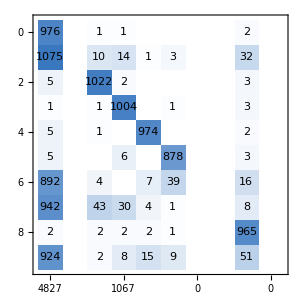
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[finalnet,testData,"ConfusionMatrixPlot"]
```

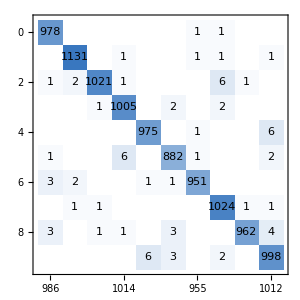
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[finalLeNet,testData,"ConfusionMatrixPlot"]
```

```mathematica
TP=NetMeasurements[finalnet,testData,"TruePositiveRate"]
```

<|0→0.995918,1→0.,2→0.99031,3→0.994059,4→0.991853,5→0.984305,6→0.,7→0.,8→0.99076,9→0.|>

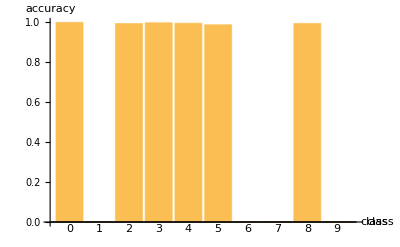

```mathematica
BarChart[List@@@TP,AxesLabel->{"class","accuracy"},ChartLabels->{"0","1","2","3","4","5","6","7","8","9"}]
```

```mathematica
TPLeNet=NetMeasurements[finalLeNet,testData,"TruePositiveRate"]
```

<|0→0.997959,1→0.996476,2→0.989341,3→0.99505,4→0.992872,5→0.988789,6→0.992693,7→0.996109,8→0.98768,9→0.989098|>

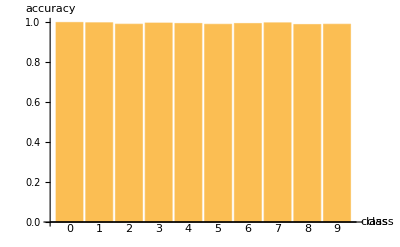

```mathematica
BarChart[List@@@TPLeNet,AxesLabel->{"class","accuracy"},ChartLabels->{"0","1","2","3","4","5","6","7","8","9"}]
```

```mathematica
(*Visualisation kernels trained network*)
finalnet
```

NetChain[<>]

```mathematica
layer1=NetExtract[finalnet,1]
```

ConvolutionLayer[<>]

```mathematica
w1=NetExtract[layer1,"Weights"]
```

NumericArray[…]

```mathematica
Map[ImageAdjust@Image[#,Interleaving->False]&,Normal@w1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Kernels of 1st layer; 6 of them, each one 5 x 5*)
```

```mathematica
layer4=NetExtract[finalnet,4]
```

ConvolutionLayer[<>]

```mathematica
w4=NetExtract[layer4,"Weights"]
```

NumericArray[…]

```mathematica
w4[[1,2]]//Normal
```

{{0.226756,0.147053,0.0336188,0.36649,0.696924},{-0.0247692,-0.100841,0.102188,0.130611,0.219267},{0.0291581,-0.00686158,0.0366296,0.0882364,0.385213},{-0.136417,-0.0680356,0.0554773,0.158529,0.195166},{-0.119323,-0.260646,-0.141436,0.0815591,0.352999}}

```mathematica
ImageAdjust[Image[w4[[1,2]]]]
```

-Graphics-

```mathematica
Table[ImageAdjust[Image[w4[[k1,k2]]]],{k1,1,12},{k2,1,6}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
(*These are the kernels of the 2nd convolutional layer: 6 x 12, each of size 5 x 5*)
```

```mathematica
(*Visualisation of feature maps when we input one example image to the network*)
i1=inputExEnc; (*Example input image (encoded)*)
```

```mathematica
o1=layer1[i1];
```

```mathematica
(*Output of convolutional layer 1*)
layers=Information[finalnet,"Layers"]
```

<|{1}→ConvolutionLayer[<>],{2}→ElementwiseLayer[<>],{3}→PoolingLayer[<>],{4}→ConvolutionLayer[<>],{5}→ElementwiseLayer[<>],{6}→PoolingLayer[<>],{7}→FlattenLayer[<>],{8}→LinearLayer[<>],{9}→ElementwiseLayer[<>],{10}→SoftmaxLayer[<>]|>

```mathematica
o1=layers[{1}][i1];
```

```mathematica
Dimensions[o1]
```

{6,24,24}

```mathematica
Magnify[Table[ImageAdjust[Image[o1[[k]]]],{k,1,6}],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fnet2=NetTake[finalnet,2](*Just take 2 layers from the trained network so that we can see the output in the hidden layers*)
```

NetChain[<>]

```mathematica
o2=fnet2[i1];
```

```mathematica
Magnify[Table[ImageAdjust[Image[o2[[k]]]],{k,1,6}],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*These are the feature maps in the first convolutional layer (after activation)*)
```

```mathematica
fnet3=NetTake[finalnet,3]
```

NetChain[<>]

```mathematica
o3=fnet3[i1];
```

```mathematica
Magnify[Table[ImageAdjust[Image[o3[[k]]]],{k,1,6}],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*These are the pooled featured maps after the 1st convolutional layer*)

fnet5=NetTake[finalnet,5]
```

NetChain[<>]

```mathematica
o5=fnet5[i1];
```

```mathematica
Dimensions[o5]
```

{12,8,8}

```mathematica
Magnify[Table[ImageAdjust[Image[o5[[k]]]],{k,1,12}],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*These are the feature maps in the second convolutional layer, after activation*)
fnet6=NetTake[finalnet,6]
```

NetChain[<>]

```mathematica
o6=fnet6[i1];
```

```mathematica
Magnify[Table[ImageAdjust[Image[o6[[k]]]],{k,1,12}],3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fnet7=NetTake[finalnet,7]
```

NetChain[<>]

```mathematica
o7=fnet7[i1];
```

```mathematica
Dimensions[o7]
```

{192}

```mathematica
o7r=ArrayReshape[o7,{192,1}];
```

```mathematica
Magnify[ImageAdjust[Image[o7r]],3]
```

-Graphics-

```mathematica
fnet9=NetTake[finalnet,9]
```

NetChain[<>]

```mathematica
o9=fnet9[i1]
```

{10.4595,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Dimensions[o9]
```

{10}

```mathematica
o9r=ArrayReshape[o9,{10,1}]
```

{{10.4595},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
Magnify[ImageAdjust[Image[o9r]],3]
```

-Graphics-

```mathematica
(*This is the final vector before the "decoder". Notice that the top element is white, corresponding to the largest value in the vector. The decoder then will select class 0. *)
```